## 1D SDE example

### Simulate dynamics

```mathematica
ClearAll[Z,dZ,dW, F]

tmax=10000;
dt=1;

D0=0.004;
a=1;

sig=Sqrt[2 D0 dt]

dW=RandomVariate[NormalDistribution[0,sig],{tmax}];

Z=Table[0,{t,1,tmax}];
Length[Z];
dZ=Table[0,{t,1,tmax}];


F[x_]:=dt  *a*(-0.2x+1.2x^3-x^5);

(* generate equally spaced time series data *)
For[t=1, t<tmax, t++,

dZ[[t]] = F[Z[[t]] ]+dW[[t]];
Z[[t+1]]=Z[[t]]+dZ[[t]]
];
```

0.0894427

### plot joint distributions

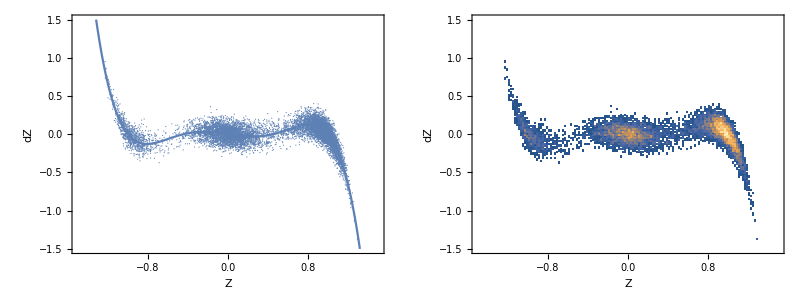

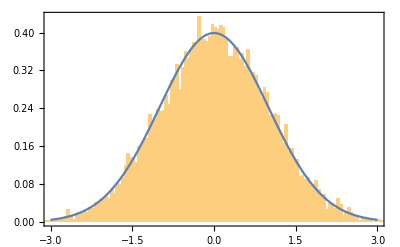

```mathematica
ListPlot[dW, PlotRange-> All];
ListPlot[dZ, PlotRange-> All];

ListPlot[Transpose[{dW,dZ}], PlotRange-> All];

p1=ListPlot[Transpose[{Z,dZ}],  
Frame-> True,
FrameLabel->{"Z","dZ"},
AspectRatio-> 1,
 PlotRange-> {{-1.5,1.5},dt{-1.5,1.5}},
ImageSize-> 300];

p2=Plot[F[z],{z,-1.5,1.5},  
Frame-> True,
FrameLabel->{"Z","dZ"},
AspectRatio-> 1,
 PlotRange-> {{-1.5,1.5},{-1.5,1.5}},
ImageSize-> 300];

p12=Show[p1,p2];

h1=DensityHistogram[Transpose[{Z,dZ}],Sqrt[tmax],"PDF",
PlotRange-> {{-1.5,1.5},{-1.5,1.5}},
FrameLabel->{"Z","dZ"},
ImageSize-> 300
];

TableForm[{{p12,h1}}]

p3=Histogram[(dZ-F[Z])/sig,Sqrt[tmax],"PDF", PlotRange-> All];
p4=Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}, PlotRange-> All];

p34=Show[p3,p4, PlotRange->{{-3,3},All}, Frame-> True]
```

## 2d SDE example

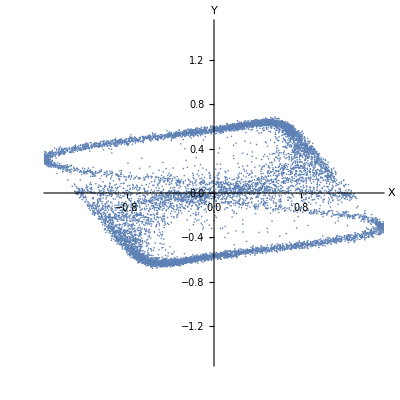

-Graphics3D-

```mathematica
ClearAll[Z,dZ,dW, F]

tmax=10000;
dt=1;


a=1;
DX=0.0004;
DY=0.0001;

sigX=Sqrt[2 DX dt];
sigY=Sqrt[2 DY dt];

dWX=RandomVariate[NormalDistribution[0,sigX],{tmax}];
dWY=RandomVariate[NormalDistribution[0,sigY],{tmax}];

T=Table[t,{t,1,tmax}];
X=Table[0,{t,1,tmax}];
Y=Table[0,{t,1,tmax}];

Length[X];
dX=Table[0,{t,1,tmax}];
dY=Table[0,{t,1,tmax}];


FX[x_,y_]:=dt  *a*((x-y)-x^3);
FY[x_,y_]:=dt  *a*(0.2(y+x)-y^3);

(* generate equally spaced time series data *)
For[t=1, t<tmax, t++,

dX[[t]]=FX[ X[[t]] , Y[[t]]  ] +dWX[[t]];
dY[[t]]=FY[ X[[t]] , Y[[t]]  ] +dWY[[t]];

X[[t+1]]=X[[t]]+dX[[t]];
Y[[t+1]]=Y[[t]]+dY[[t]];

];

p0=ListPlot[Transpose[{X, Y}],  
AxesLabel->{"X","Y"},
AspectRatio-> 1,
 PlotRange-> {{-1.5,1.5},{-1.5,1.5}}
]

pmax=1000;
ptab=Table[{T[[p]],X[[p]], Y[[p]]},{p,1,pmax}];

p0=ListLinePlot3D[ptab,  
AxesLabel->{"t","X","Y"},
AspectRatio-> 1,
 PlotRange-> {All,{-1.5,1.5},{-1.5,1.5}},
ColorFunctionScaling->True,
ColorFunction->Function[{t,x,y},Hue[t]]
]
```

### plot joint distributions

```mathematica
myPlotRange= {{-1.75,1.75},{-1,1},{-3,3}};

p1=ListPointPlot3D[Transpose[{X, Y, dX}],  
AxesLabel->{"X","Y", "dX"},
AspectRatio-> 1,
 PlotRange-> myPlotRange,
ImageSize-> 300];

p2=Plot3D[FX[x,y],{x,-2,2},{y,-1.,1.},  
AxesLabel->{"X","Y"},
AspectRatio-> 1,
 PlotRange-> myPlotRange,
ImageSize-> 300,
PlotStyle-> Opacity[0.3],
ColorFunctionScaling->True,
ColorFunction->Function[{x,y,z},Hue[z]],
PlotTheme->"Web"
];

p12=Show[p1,p2, ImageSize-> 600]


myPlotRange= {{-2,2},{-1,1},{-1.5,1.5}};

p1=ListPointPlot3D[Transpose[{X, Y, dY}],  
AxesLabel->{"X","Y", "dY"},
AspectRatio-> 1,
 PlotRange->myPlotRange,
ImageSize-> 300];

p2=Plot3D[FY[x,y],{x,-2,2},{y,-1,1},  
AxesLabel->{"X","Y"},
AspectRatio-> 1,
 PlotRange-> myPlotRange,
ImageSize-> 300,
PlotStyle-> Opacity[0.3],
ColorFunctionScaling->True,
ColorFunction->Function[{x,y,z},Hue[z]],
PlotTheme->"Web"
];

p12=Show[p1,p2, ImageSize-> 600]
```

-Graphics3D-

-Graphics3D-